```mathematica
(* Initialisation *)
(* Evaluate before start writing "real code" *)
(* Usage e.g.: "ld [Spacekey]" becomes "⊨", so writing "a ld 5" turns into "a ⊨ 5" *) 
SetOptions[EvaluationNotebook[], 
			 InputAutoReplacements -> { (* special AceGen assignment operators: *) "ld"-> "⊨","ls"->"⊢","rd"->"⫤","rs"->"⊣",
					                                 (* brackets and symbols: *) "dbl"->"⟦","dbr"->"⟧","lcb"->"{","rcb"->"}","lsb"->"[","rsb"->"]","->"->"→",
					                                 (* shortcuts for starting/ending a comment block: *) "co"->"(*","cc"->"*)"
					                              }
		   ]
(* Output the current time, so we know when AceGen has been executed the last time *)
Now
```

Wed 29 May 2024 16:47:17GMT+2

```mathematica
(* Clear all old variables initially to have a fresh start *)
ClearAll["Global`*"] 
(* Start AceGen *) 
<<AceGen`;
(* Name of the to be created subroutine/function in the below specified programming language *)
NAME = "IfConditions_Nested";
(* Name of the AceGen session "NAME", specify the programming language "Language"={C++,Matlab,Fortran,...}, and the execution mode "Mode"={Optimal,Prototype,Debug,Plain} *)
(* @note Changing the output programming language can be very simple here, so feel free to take advantage of all the available languages. For instance, first export to a Matlab-code, because you can quickly and easily debug and check the code and its output. *) 
SMSInitialize[NAME,"Language"-> "Matlab","Mode"-> "Optimal"]; 
(* Start a module, which represents the to be created function, with name "NAME" and the specified input and output arguments *) 
SMSModule[NAME,Real[ xInput$$,y1Output$$, Dy1DxOutput$$,y2Output$$, Dy2DxOutput$$ ,y3Output$$, Dy3DxOutput$$ ,y4Output$$, Dy4DxOutput$$  ],
		"Input"-> { xInput$$ },
		"Output" -> { y1Output$$, Dy1DxOutput$$,y2Output$$, Dy2DxOutput$$,y3Output$$, Dy3DxOutput$$,y4Output$$, Dy4DxOutput$$ }
	       ];
(* Input declaration by copying AceGen input variables to Mathematica variables *)
x ⊨ SMSReal[ xInput$$ ];
```

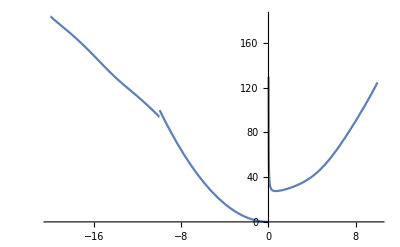

```mathematica
(* Compute the output variable y based on the input x, here using some arbitrary expression *) 
ypart1[x_]:=25+x^2+1/x+Sin[x];
ypart2[x_]:=-9*x+Sin[x]+SMSSqrt[-x];
ypart3[x_]:=x^2;
y[x_]:=If[x>=0,ypart1[x],If[x<-10,ypart2[x],ypart3[x]]];
Plot[y[xTest],{xTest,-20,10}]
```

```mathematica
(* Form 1 *) 
y1 ⊨ SMSIf[x>=0,ypart1[x], SMSIf[x<-10,ypart2[x],ypart3[x]]];
```

```mathematica
(* Form 2 *) 
SMSIf[ x>=0];
    y2 ⫤ypart1[x];
SMSElse[];
    SMSIf[ x<-10];
        y2 ⊣ypart2[x];
    SMSElse[];
        y2 ⊣ ypart3[x];
    SMSEndIf[{y2}];
SMSEndIf[{y2}];
```

```mathematica
(* Form 3 *) 
y3 ⫤ 0;
SMSIf[ x>=0];
    y3 ⊣ypart1[x];
SMSElse[];
   SMSIf[ x<-10];
        y3 ⊣ ypart2[x];
    SMSElse[];
        y3 ⊣ypart3[x];
    SMSEndIf[{y3}];
SMSEndIf[{y3}];
(* Form 4 *) 
SMSIf[x>=0];
	y4 ⫤ ypart1[x];
SMSEndIf[y4];
SMSIf[x<-10];
	y4⊣ ypart2[x];
SMSEndIf[y4];
SMSIf[x<0 && x>=-10];
	y4⊣ypart3[x];
SMSEndIf[y4];
```

```mathematica
SMSExport[y1 ,y1Output$$];
Dy1 Dx⊨ SMSD[y1,x]; 
SMSExport[Dy1 Dx, Dy1DxOutput$$];
```

```mathematica
SMSExport[y2 ,y2Output$$];
Dy2 Dx⊨ SMSD[y2,x]; 
SMSExport[Dy2 Dx, Dy2DxOutput$$];
```

```mathematica
SMSExport[y3 ,y3Output$$];
Dy3 Dx⊨ SMSD[y3,x]; 
SMSExport[Dy3 Dx, Dy3DxOutput$$];
```

```mathematica
SMSExport[y4 ,y4Output$$];
Dy4 Dx⊨ SMSD[y4,x]; 
SMSExport[Dy4 Dx, Dy4DxOutput$$];
```

```mathematica
(* Output the time at the end of the execution *)
Now 
(* Write output file containing all the above defined functions introduced by SMSModule *)
(* Create output file named "NAME", '"LocalAuxiliaryVariables" -> True' is a command to exclude the AceGen internal array "v" from the list of input and output arguments of the created subroutine *)
SMSWrite[NAME,"LocalAuxiliaryVariables" -> True]; 
(* Print the content of the just created file on screen (sensible only for small file sizes) *)
FilePrint[ StringJoin[NAME,Which[SMSLanguage=="Fortran",".f",
							   SMSLanguage=="Matlab",".m",
							   SMSLanguage=="C++",".cpp",
							   SMSLanguage=="C",".c"
							 ]
					]
		   ]
```

Wed 29 May 2024 16:47:18GMT+2

File: IfConditions_Nested.m  Size: 2207  Time: 1
Method | IfConditions_Nested
No.Formulae | 47
No.Leafs | 287

%**************************************************************
%* AceGen    7.505 Linux (16 Aug 22)                          *
%*           Co. J. Korelc  2020           29 May 24 16:47:19 *
%**************************************************************
% User     : Full professional version
% Notebook : AceGen-SMSIf_Nested
% Evaluation time                 : 1 s     Mode  : Optimal
% Number of formulae              : 47      Method: Automatic
% Subroutine                      : IfConditions_Nested size: 287
% Total size of Mathematica  code : 287 subexpressions
% Total size of Matlab code      : 1297 bytes 

%*********************** F U N C T I O N **************************
function[y1Output,Dy1DxOutput,y2Output,Dy2DxOutput,y3Output,Dy3DxOutput,y4Output,Dy4DxOutput]=IfConditions_Nested(xInput);
persistent v;
if size(v)<189
  v=zeros(189,'double');
end;
v(1)=xInput;
b5=v(1)<-10e0;
b2=v(1)>=0;
if(b2)
 v(27)=-(1/Power(v(1),2))+2e0*v(1)+cos(v(1));
 v(9)=25e0+1/v(1)+(v(1)*v(1))+sin(v(1));
 v(28)=v(27);
 v(4)=v(9);
else;
 if(b5)
  v(42)=sqrt(-v(1));
  v(29)=-9e0-1/(2e0*v(42))+cos(v(1));
  v(12)=-9e0*v(1)+v(42)+sin(v(1));
  v(30)=v(29);
  v(7)=v(12);
 else;
  v(31)=2e0*v(1);
  v(13)=(v(1)*v(1));
  v(30)=v(31);
  v(7)=v(13);
 end;
 v(28)=v(30);
 v(4)=v(7);
end;
if(b2)
 v(34)=v(27);
 v(10)=v(9);
else;
 if(b5)
  v(34)=v(29);
  v(10)=v(12);
 else;
  v(34)=v(31);
  v(10)=v(13);
 end;
end;
v(37)=0;
v(14)=0;
if(b2)
 v(37)=v(27);
 v(14)=v(9);
else;
 if(b5)
  v(37)=v(29);
  v(14)=v(12);
 else;
  v(37)=v(31);
  v(14)=v(13);
 end;
end;
if(b2)
 v(40)=v(27);
 v(22)=v(9);
else;
end;
if(b5)
 v(43)=sqrt(-v(1));
 v(40)=-9e0-1/(2e0*v(43))+cos(v(1));
 v(22)=-9e0*v(1)+v(43)+sin(v(1));
else;
end;
if(v(1)<0 && v(1)>=-10e0)
 v(40)=2e0*v(1);
 v(22)=(v(1)*v(1));
else;
end;
y1Output=v(4);
Dy1DxOutput=v(28);
y2Output=v(10);
Dy2DxOutput=v(34);
y3Output=v(14);
Dy3DxOutput=v(37);
y4Output=v(22);
Dy4DxOutput=v(40);


function [x]=SMSKDelta(i,j)

if (i==j) , x=1; else x=0; end;

end

function [x]=SMSDeltaPart(a,i,j,k)

l=round(i/j);

if (mod(i,j) ~= 0 | l>k) , x=0; else x=a(l); end;

end

function [x]=Power(a,b)

x=a^b;

end

function [x]=SMSTernaryOperator(a,b,c)

if (c) , x=a; else x=b; end;

end

end